# Trabalho em Grupo(Opcional) Campo Elétrico

# Fundamentos de Física 3 - 2023/2 Aluno Caio Cordeiro Jácome

### 1. Use o software Wolfram Mathematica para calcular a integral que resulta na expressão do campo elétrico E⃗(ρ, θ, z), para uma linha de cargas infinita, com densidade linear constante λ0 é : E⃗(ρ, θ, z) = 1/(2 π ε0) λ0/ρ ρ̂ Use o software Wolfram Mathematica para fazer gráfico de : a) módulo do campo elétrico E⃗ (ρ)*ρ; b) campo vetorial de E⃗ no plano; c) campo vetorial de E⃗ no espaço 3 D . Dica : considere nos gráficos (2 π ε0) igual a 1 e λ0 também igual a 1.

#### Calculando a integral:

```mathematica
CampoEletrico = Integrate[(1/ρ),ρ];
Print[CampoEletrico]
```

Log[ρ]

#### Módulo do Campo ElétricoE⃗ (ρ)*ρ;

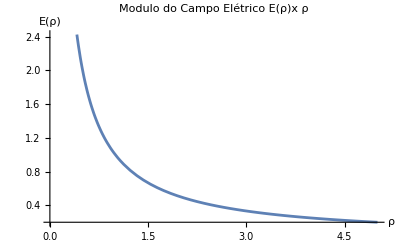

```mathematica
Plot[1/ρ,{ρ,0.01,5},
AxesLabel->{"ρ", "E(ρ)"},
PlotLabel->"Modulo do Campo Elétrico E(ρ)x ρ"]
```

#### Campo vetorial de E⃗ no plano;

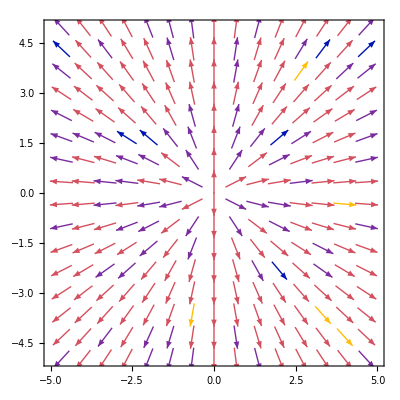

```mathematica
coordX = 1/Sqrt[x^2+y^2]*x;
coordY = 1/Sqrt[x^2+y^2]*y;
VectorPlot[{coordX, coordY},{x, -5, 5}, {y, -5, 5}, VectorPoints -> 15,
 VectorScale -> {0.05, Automatic, None}]
```

#### Campo vetorial de E⃗ no espaço 3 D .

```mathematica
VectorPlot3D[{coordX,coordY, z},{x, -5, 5}, {y, -5, 5}, {z, -5, 5},
 VectorPoints -> 10, VectorScale -> {0.05, Automatic, None}]
```

-Graphics3D-

### 2.Use o software Wolfram Mathematica para calcular a integral na expressão do campo elétricoE⃗ , sobre um ponto z arbitrário do eixo do anel carregado (usualmente eixo z) com uma densidade de cargas linear constante : E(z) = 1/(4 π ε0)(Q z)/((z^2+R^2)^(3/2)) Onde Q é carga elétrica total do anel e R é o raio do anel. Use o software Wolfram Mathematica para fazer gráfico de : a) E(z) × z; b) E(z, R) × (z, R). Dica : considere no gráfico (4 π ε0) igual a 1, além de Q também igual a 1 (e R igual a 1 na letra (a)).

#### E(z) x z

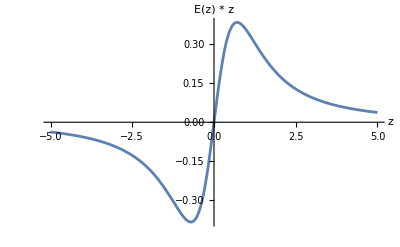

```mathematica
Plot[z/((z^2) + 1)^(3/2),{z,-5,5},AxesLabel -> {"z", "E(z) * z"}]
```

#### E (z, R) * (z, R)

```mathematica
Plot3D[z/((z^2) + (R^2))^(3/2), {z, -5,5}, {R, 0.1, 10}, AxesLabel -> {"z", "R", "E(z, R) * z"}]
```

-Graphics3D-